```mathematica
temp = N[E, 100]
```

2.718281828459045235360287471352662497757247093699959574966967627724076630353547594571382178525166427

```mathematica
Precision[]
```

∞

```mathematica
BlochWignerLi2[z_]:=Im[PolyLog[2,z]]+Arg[1-z]Log[Abs[z]];
ClearAll[t1];
(* compute conifold period using Marcos' formula 1.29, compare to infinite sum *)
With[{λ=1,Nn=100,Pre=50},uval=Sort[-1/ut/.NSolve[-27-ut^3+36 ut λ+ut^4 λ-8 ut^2 λ^2+16 λ^3==0,ut,WorkingPrecision->Pre],Abs[x_]&][[1]];
bval=(t1-Sqrt[6 X0])/(t1+Sqrt[6 X0])/.X0->t1^2/2+t1/.t1->-2+Sqrt[1+12 λ uval^2];

Print["u = ",uval,"(P: ", Precision[uval], ") \nb = ",bval,"(P: ", Precision[bval], ")\nt1 = ",-2+Sqrt[1+12 λ uval^2], "(P: ", Precision[-2+Sqrt[1+12 λ uval^2]], ")"];

Pexact=1/2/Pi(5 BlochWignerLi2[b]-4 BlochWignerLi2[b^2]+BlochWignerLi2[b^3])-1/2/Pi Log[Abs[λ]](Arg[1/b^2]-Arg[b])/.b->bval;
Print[Precision[Pexact]];

Pseries = Log[-ut]-Sum[If[3k+2l>=2,(3k+2l-1)!/((k+l)!(k!)^2l!)(λ)^l (-ut)^(-3k-2l),0],{k,0,Nn},{l,0,Nn}]/.ut->-1/uval;
Print[Precision[Pseries]];
N[{Pexact, Pseries}, Pre]
]
```

u = 0.26318526921874357906535706027814525189676702802574(P: 50.) 
b = -0.7251497610490148665275651524636838940601276942613+0.6885911878978387285805195905580644422553067984718 ⅈ(P: 49.2662)
t1 = -0.64678241542429310724842125241159423811328200325712(P: 50.0224)

48.0535

49.6449

{1.15732210074666531243235075733319062483391568725,1.157955630018386141836781859567451106273049274607}

## ChatGPT

```mathematica
Clear[RichardsonTable,RichardsonExtrapolate];

(*Build the full Richardson tableau.vals={A(h),A(h/r),A(h/r^2),...} p=leading error exponent r=refinement ratio (default 2)*)
RichardsonTable[vals_List,p_?NumericQ,r_:2]:=Module[{m=Length[vals],t,k,i},t=ConstantArray[0,{m,m}];
t[[All,1]]=N[vals, 200];(*first column=raw approximations*)Do[Do[(*R_{k,i}=R_{k-1,i+1}+(R_{k-1,i+1}-R_{k-1,i})/(r^(p k)-1)*)t[[i,k+1]]=t[[i+1,k]]+(t[[i+1,k]]-t[[i,k]])/(r^(p k)-1),{i,1,m-k}],{k,1,m-1}];
t];

(*Return the best extrapolated value (and optionally the table)*)
RichardsonExtrapolate[vals_List,p_?NumericQ,r_:2]:=Module[{t=RichardsonTable[vals,p,r]},<|"BestEstimate"->t[[1,Length[vals]]],"Table"->t|>];
```

```mathematica
Clear[RichardsonExtrapolateCompiled];

RichardsonExtrapolateCompiled=Compile[{{vals,_Real,1},{p,_Real},{r,_Real}},Module[{m=Length[vals],t,k,i},t=Table[0.,{m},{m}];
t[[All,1]]=vals;
For[k=1,k<=m-1,k++,For[i=1,i<=m-k,i++,t[[i,k+1]]=t[[i+1,k]]+(t[[i+1,k]]-t[[i,k]])/(r^(p k)-1.);];];
{t[[1,m]],t}],CompilationTarget->"C",RuntimeOptions->"Speed"];
```

```mathematica
Clear[SPartial];
SPartial[N_Integer]:=Sum[(-1)^(k+1)/k,{k,1,N}];   (*or your own fast implementation*)
```

```mathematica
n0=100;          (*base N*)
levels=5;           (*number of Richardson levels/number of vals*)
Ns=n0*2^Range[0,levels-1];

vals=N[Table[SPartial[Ns[[j]]],{j,Length[Ns]}], 200];
```

```mathematica
vals[[3]]
```

0.69189874305506255795076719902489762189503536754851329054098112481578583845631673562738681363793744823586754272168889649440190930153994003719686279717717078054441658514768197631514604409545443290714392

```mathematica
(*p=exponent in the leading error term:for many p-series with p>1,error~const/N,so try p=1 first*)
res=RichardsonExtrapolate[vals,1,2];

bestEstimate=res["BestEstimate"];
richTable=res["Table"];
```

```mathematica
N[bestEstimate-Log[2],500]
```

4.72723503609728762824740962263695636900565906609521936871801649194955163662090247613471419310787487213016137191813232020062397006133714734516003112828958549667114982848528568486199898×10^-16

```mathematica
vals
```

{0.68817217931019520324464588269348406593837030274099782351763152441038775097468313878990510503877912345244824953423809624010318986230624791624523293600542046319965143617672474790687084884262026380431498,0.69065343048182421525226872147260847892842811982179143128843798813565877249728968494427653294367851028740576224876592672903139591382673991733877585696968097184150592862281405325413216947050725252357753,0.69189874305506255795076719902489762189503536754851329054098112481578583845631673562738681363793744823586754272168889649440190930153994003719686279717717078054441658514768197631514604409545443290714392,0.69252257118464013458965010494309542546365677818978674365556525500413619747899200587337357039949996664449474851945843246879046505688153188246252222367270070081420571629837181414360275279828468093399226,0.69283477821617623594580513291383882163437571565247102187429513961429608962302829970608614473678607761432550845124431832366338362613230546042301368474068375338906845328171272684130972561320664071377627}

## Mathematica accel

```mathematica
ClearAll[aN]
```

```mathematica
aN[u_,m_,n_]:=aN[u,m,n]=Sum[If[EvenQ[n-3k], (n-1)!/(n/2-k/2)!/(k!)^2/(n/2-3k/2)!m^(n/2-3k/2)u^n,0], {k, 0, Ceiling[n/3]}];
```

```mathematica
aN[u/.u0,1,1000]//AbsoluteTiming
```

{0.006292,2.944906866630581776204167534893545247947071780771435737380927096219604480306481153855182702267328×10^-7}

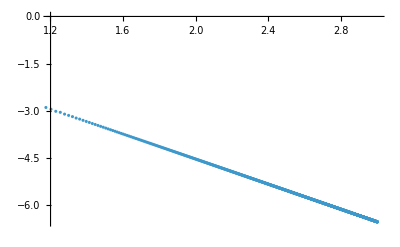

```mathematica
Table[{Log10[n], Log10[aN[u/.u0, 1, n]]}, {n, 2, 1000}];
ListPlot[%]
```

```mathematica
tN[u_,m_,N_]:=-Log[u]-Sum[aN[u,m,n], {n,2,N}];
```

```mathematica
Table[aN[u/.u0,1,n], {n,2,2000}];
sums = -Log[u/.u0]-Accumulate[%];
```

```mathematica
NSolve[m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4==0/.{m->1}, u, WorkingPrecision->100]
```

{{u→-3.025715204493386203960987268171489359218246757524544794327270504015175963360670269419365276058026471},{u→-0.2550986687263150511885485324169643099756237716142341628963450215473033536170516076188092099311345924-0.221552814358828300551389985511187642051434198821165292729717138057468737028301577902814798809376111 ⅈ},{u→-0.2550986687263150511885485324169643099756237716142341628963450215473033536170516076188092099311345924+0.221552814358828300551389985511187642051434198821165292729717138057468737028301577902814798809376111 ⅈ},{u→0.2631852692187435790653570602781452518967670280257403928472332743825099433220462119297109686475683835}}

```mathematica
u0 = {u->0.2631852692187435790653570602781452518967670280257403928472332743825099433220462119297109686475683835161379415386879`100.};
```

1.1573221007466653124323507573331906

```mathematica
target=1.1573221007466653124323507573331906
```

1.157322100746665312432350757333191

```mathematica
tN[u/.u0, 1, 500]
```

1.15791049389304797552895589419817714106764729757997098814048516912495856116227528556318549746484965

```mathematica
Clear[estimateP]
estimateP[u_,m_,n0_Integer?Positive]:=Module[{a1,a2,a3,p},
a1=tN[u,m,n0];
a2=tN[u,m,2 n0];
a3=tN[u,m,4 n0];
p/. First@FindRoot[(a1-a2)/(a2-a3)==(1-2^-p)/(2^-p-4^-p),{p,1}]]
```

```mathematica
estimateP[u/.u0,1,500]
```

0.998305

```mathematica
tRich[N_, u_, m_, p_]:=Module[{},
aN = tN[u, m, N];
a2N = tN[u,m, 2N];
(2^p a2N-aN)/(2^p-1)
];
```

```mathematica
data = Table[{p, Abs[tRich[200, u/.u0, 1, p]-target]}, {p, 1, 50}];
```

$Aborted

## Second try

```mathematica
ClearAll[aN];
```

```mathematica
aN[u_,m_,n_]:=aN[u,m,n]=Sum[If[EvenQ[n-3k], (n-1)!/(n/2-k/2)!/(k!)^2/(n/2-3k/2)!m^(n/2-3k/2)u^n,0], {k, 0, Ceiling[n/3]}];
```

```mathematica
tN[u_,m_,N_]:=-Log[u]-Sum[aN[u,m,n], {n,2,N}];
```

```mathematica
Table[aN[u/.u0,1,n], {n,2,2000}];
sums = -Log[u/.u0]-Accumulate[%];
```

```mathematica
target=1.1573221007466653124323507573331906
```

1.157322100746665312432350757333191

```mathematica
Last[sums]
```

1.15746937191257021321776205601801334342491728167473121815883886846603377425112827457454855384686895

```mathematica
Nn+i == Length[sums]
```

```mathematica
Length[sums]
```

1999

```mathematica
With[{Nn=1970, p=1},
Print["d=",Length[sums]-Nn+1];
subs = With[{d=Length[sums]-Nn+1},
Table[alp[i]->
(-1)^i(Nn+i)^(p+d-2)/i!/(d-1-i)!/Sum[(-1)^j (Nn+j)^(p+d-2)/j!/(d-1-j)!, {j, 0, d-1}]
, {i,0,d-1}]
];
Print[N[subs]];
Sum[alp[i]*sums[[Nn+i]], {i, 0, Length[sums]-Nn}]-target/.subs
]
```

d=30

{alp[0.]→-3.91725×10^64,alp[1.]→1.15285×10^66,alp[2.]→-1.6379×10^67,alp[3.]→1.49594×10^68,alp[4.]→-9.86757×10^68,alp[5.]→5.00679×10^69,alp[6.]→-2.03233×10^70,alp[7.]→6.77636×10^70,alp[8.]→-1.89103×10^71,alp[9.]→4.47755×10^71,alp[10.]→-9.08726×10^71,alp[11.]→1.59277×10^72,alp[12.]→-2.42438×10^72,alp[13.]→3.21706×10^72,alp[14.]→-3.73079×10^72,alp[15.]→3.78571×10^72,alp[16.]→-3.36123×10^72,alp[17.]→2.60815×10^72,alp[18.]→-1.76432×10^72,alp[19.]→1.03646×10^72,alp[20.]→-5.25838×10^71,alp[21.]→2.28666×10^71,alp[22.]→-8.43711×10^70,alp[23.]→2.60546×10^70,alp[24.]→-6.6091×10^69,alp[25.]→1.34118×10^69,alp[26.]→-2.09356×10^68,alp[27.]→2.36021×10^67,alp[28.]→-1.71052×10^66,alp[29.]→5.98456×10^64}

0.

```mathematica
Table[{Length[sums]-Nn+1, With[{p=1},
Print["d=",Length[sums]-Nn+1];
subs = With[{d=Length[sums]-Nn+1},
Table[alp[i]->
(-1)^i(Nn+i)^(p+d-2)/i!/(d-1-i)!/Sum[(-1)^j (Nn+j)^(p+d-2)/j!/(d-1-j)!, {j, 0, d-1}]
, {i,0,d-1}]
];
Print[N[subs]];
Sum[alp[i]*sums[[Nn+i]], {i, 0, Length[sums]-Nn}]-target/.subs
]}, {Nn, 1950, Length[sums]}]
```

```mathematica
target
```

1.157322100746665312432350757333191

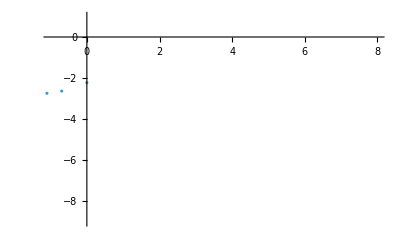

```mathematica
data = Table[{-Log[n], Log[sums[[n]]-target]}, {n, 1, Length[sums]}];
ListPlot[%,
PlotRange->{{-1,8}, {-9, 1}}
]
```

```mathematica
Fit[data, {1,x},x]
```

-1.35049238188143867537290071074+0.981523515618094301800918634925 x